```mathematica
x1[n_]:= 1/2(1-Cos[n]);
```

```mathematica
t1[n_]:=1/2(n-Sin[n]);
```

```mathematica
x2[n_]:= 1/2(Cosh[n]-1);
```

```mathematica
t2[n_]:=1/2(Sinh[n]-n);
```

```mathematica
step = 1;
```

```mathematica
range = 10;
```

```mathematica
list1 =Table[N/@{t1[n],x1[n],n},{n,0,range,step}];
```

```mathematica
list2 =Table[{t2[n],x2[n],n},{n,0,range,step}];
```

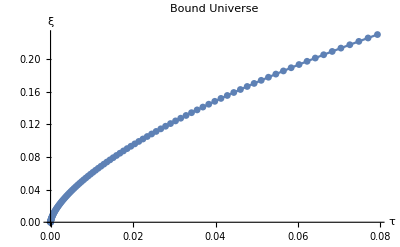

```mathematica
ListPlot[Table[Part[list1[[i]],{1,2}],{i,1,Length[list1]}],Joined->True,PlotMarkers->{Automatic,7},PlotLabel->"Bound Universe",AxesLabel->{"τ","ξ"}]
```

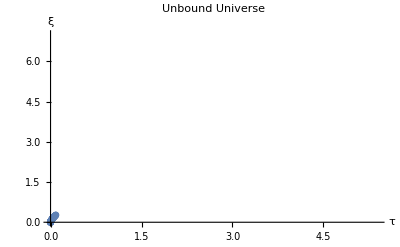

```mathematica
ListPlot[Table[Part[list2[[i]],{1,2}],{i,1,Length[list1]}],Joined->True,PlotMarkers->{Automatic,7},PlotLabel->"Unbound Universe",AxesLabel->{"τ","ξ"},PlotRange->{{0,5.39},{0,7}}]
```

```mathematica
Table1 =Insert[list1,{"τ","ξ","η"},1];
```

```mathematica
Table2 =Insert[N[list2],{"τ","ξ","η"},1];
```

```mathematica
Grid[Table2,Frame->All]
```

τ | ξ | η
0. | 0. | 0.
0.0876006 | 0.27154 | 1.
0.81343 | 1.3811 | 2.
3.50894 | 4.53383 | 3.
11.645 | 13.1541 | 4.
34.6016 | 36.605 | 5.
97.8566 | 100.358 | 6.
270.658 | 273.659 | 7.
741.239 | 744.74 | 8.
2021.27 | 2025.27 | 9.
5501.62 | 5506.12 | 10.

```mathematica
Series[Sin[x],x]
```

Series::sspec: Series specification x is not a list with three elements.

```mathematica
Series[x-Sin[x],{x,0,3}]
```

x^3/6+O[x]^4

```mathematica
Series[-(x-Sinh[x]),{x,0,3}]
```

x^3/6+O[x]^4

```mathematica
?Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.